```mathematica
ClearAll["Global`*"]
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]



QFIperPhotonEP[Nmodes_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


QFIperPhotonEPAnal[Nmodes_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]

QFInoDisp[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/2 (Tr[Σout]-2 Nmodes))//FullSimplify
]


LeadingOrderCheck[cov_,disp_,n_,Nmodes_]:=Module[{M,d,G,EOM,DM,DMq,CovForm,DispForm,nForm},
M=Nmodes;
d=Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DMq=CovarBasis[Nmodes].DM.Transpose[CovarBasis[Nmodes]];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify;
Print["leading order covariant ",CovForm];
Print[Coefficient[cov,t^(4M-4)]==CovForm//FullSimplify];

DispForm=(2 1)/((M-1)!)^4 d.MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].d//FullSimplify;
Print["leading order displacement ",DispForm];
Print[Coefficient[disp,t^(4M-4)]==DispForm//FullSimplify];

nForm=1/(2 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]]+d.MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].d)//FullSimplify;
Print["leading order mean photon number  ",nForm];
Print[Coefficient[n,t^(2M-2)]==nForm//FullSimplify];
]

MapThread[Themes`AddThemeRules["LogGrid",#,GridLines->#2,Frame->True]&,{{LogPlot|ListLogPlot,LogLinearPlot|ListLogLinearPlot,LogLogPlot|ListLogLogPlot},{{Automatic,logticks},{logticks,Automatic},logticks}}];
```

4+4 t^2 χ^2

4 (1+t^2 χ^2)^2

1+10 t^2 χ^2+8 t^4 χ^4+(16 t^6 χ^6)/9+(9 (9+4 t^2 χ^2))/(27+18 t^2 χ^2+4 t^4 χ^4)

(4 (108+315 t^2 χ^2+t^4 χ^4 (387+237 t^2 χ^2+77 t^4 χ^4+13 t^6 χ^6+t^8 χ^8)))/(9 (12+5 t^2 χ^2+t^4 χ^4))

{-√(ξ1^2-ω^2),√(ξ1^2-ω^2)}

(2 (ξ1^2-2 ω^2+ξ1^2 Cosh[2 t √(ξ1^2-ω^2)]))/(ξ1^2-ω^2)

{ⅈ √3,-ⅈ √3}

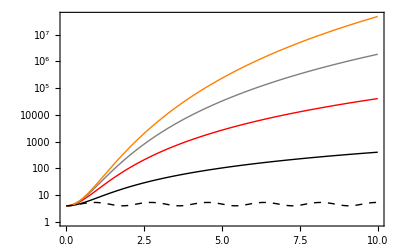

```mathematica
Clear[g,χ,ξ1,ω]
FEP2=QFInoDisp[2,χ,χ]
FEP3=QFInoDisp[3,χ,χ]
FEP4=QFInoDisp[4,χ,χ]
FEP5=QFInoDisp[5,χ,χ]


Nmodes=1;

τz=PauliMatrix[3];
τx=PauliMatrix[1];

EOM=-I(ω τz+ I ξ1 τx);
Eigenvalues[EOM]
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
F1=(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/2 (Tr[Σout]-2 Nmodes))//FullSimplify



χ=1;ξ1=1;ω=2;
Eigenvalues[EOM]
p=LogPlot[{FEP2,FEP3,FEP4,FEP5,F1},{t,0,10},PlotStyle->{Black,Red,Gray,Orange,{Black,Dashed},{Red,Dashed},{Gray,Dashed},{Orange,Dashed}},GridLinesStyle->LightGray,PlotTheme->"LogGrid",GridLines->Full]
```

```mathematica
(* Tridiagonal Toeplitz Decomposition*)
Nmodes=3;
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];

DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DM//FullSimplify//TraditionalForm
S=MatrixExp[DM t]//FullSimplify;

Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;


T1=DM[[1;;Nmodes,1;;Nmodes]]//FullSimplify;

T2=DM[[Nmodes+1;;2 Nmodes,Nmodes+1;;2 Nmodes]]//FullSimplify;
```

(0 | g+χ | 0 | 0 | 0 | 0
χ-g | 0 | g+χ | 0 | 0 | 0
0 | χ-g | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | g-χ | 0
0 | 0 | 0 | -g-χ | 0 | g-χ
0 | 0 | 0 | 0 | -g-χ | 0)

```mathematica
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Gt=Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes];

(*calculation of covariant QFI*)
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}]
x=Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify],{k,1,Nmodes},{h,1,Nmodes}];
y=Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify],{h,1,Nmodes},{k,1,Nmodes}];

Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,tr=Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//FullSimplify];

Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,nout=1/2 Tr[(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x],x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]]-Nmodes//FullSimplify];



tr==Tr[Inverse[Σin].G.Σin.G]//FullSimplify
nout==1/2 Tr[Σin]-Nmodes//FullSimplify 
Fcov=-1/2 tr-Nmodes;

Fcov/nout//FullSimplify
```

{√2 √(-g^2+χ^2),0,-√2 √(-g^2+χ^2)}

True

True

(4 (g^2-χ^2 Cosh[√2 t √(-g^2+χ^2)])^2)/((g^2-χ^2)^2)

```mathematica
qfi2=(4 g^2-2 χ^2-2 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2);
qfi3=(4 (g^2-χ^2 Cosh[√2 t √(-g^2+χ^2)])^2)/((g^2-χ^2)^2);
```

```mathematica
(* Formulas check*)

M=Assuming[{g,χ}∈Reals&&g>0&&χ>0&&χ>g,x.MatrixExp[DiagonalMatrix[λ] t].y//FullSimplify];
Mcheck=Table[Sum[((χ+g)/(χ-g))^((j-i)/2) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)]Exp[t 2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)]],{k,1,Nmodes}],{i,1,Nmodes},{j,1,Nmodes}]//FullSimplify;
Assuming[{g,χ}∈Reals&&g>0&&χ>0&&χ>g,M==Mcheck//FullSimplify]

MMTcheck=Table[Sum[((χ+g)/(χ-g))^(j-(i+l)/2) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)]  Sin[(l m π)/(Nmodes+1)]  Sin[(j m  π)/(Nmodes+1)]Exp[t 2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)]+t 2 Sqrt[χ^2-g^2] Cos[(m π)/(Nmodes+1)]],{k,1,Nmodes},{j,1,Nmodes},{m,1,Nmodes}],{i,1,Nmodes},{l,1,Nmodes}];
Assuming[{g,χ}∈Reals&&g>0&&χ>0&&χ>g,M.Transpose[M]==MMTcheck//FullSimplify]

MM2check=Table[Sum[((χ+g)/(χ-g))^(j+q-p-(i+l)/2) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)] Sin[(p m π)/(Nmodes+1)] Sin[(j m π)/(Nmodes+1)] Sin[(p n π)/(Nmodes+1)] Sin[(q n π)/(Nmodes+1)] Sin[(l r π)/(Nmodes+1)] Sin[(q r π)/(Nmodes+1)]Exp[t 2 Sqrt[χ^2-g^2] (Cos[(k π)/(Nmodes+1)]+Cos[(m π)/(Nmodes+1)]+Cos[(n π)/(Nmodes+1)]+Cos[(r π)/(Nmodes+1)])],{k,1,Nmodes},{j,1,Nmodes},{m,1,Nmodes},{q,1,Nmodes},{n,1,Nmodes},{r,1,Nmodes},{p,1,Nmodes}],{i,1,Nmodes},{l,1,Nmodes}]//FullSimplify;
Assuming[{g,χ}∈Reals&&g>0&&χ>0&&χ>g,M.Transpose[M].M.Transpose[M]==MM2check//FullSimplify]

trace=(2/(Nmodes+1))^4 Sum[((χ+g)/(χ-g))^(j+q-p-i) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)] Sin[(p m π)/(Nmodes+1)] Sin[(j m π)/(Nmodes+1)] Sin[(p n π)/(Nmodes+1)] Sin[(q n π)/(Nmodes+1)] Sin[(i r π)/(Nmodes+1)] Sin[(q r π)/(Nmodes+1)]Exp[t 2 Sqrt[χ^2-g^2] (Cos[(k π)/(Nmodes+1)]+Cos[(m π)/(Nmodes+1)]+Cos[(n π)/(Nmodes+1)]+Cos[(r π)/(Nmodes+1)])],{k,1,Nmodes},{j,1,Nmodes},{m,1,Nmodes},{q,1,Nmodes},{n,1,Nmodes},{r,1,Nmodes},{p,1,Nmodes},{i,1,Nmodes}]+(2/(Nmodes+1))^4 Sum[((χ+g)/(χ-g))^(j+q-p-i) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)] Sin[(p m π)/(Nmodes+1)] Sin[(j m π)/(Nmodes+1)] Sin[(p n π)/(Nmodes+1)] Sin[(q n π)/(Nmodes+1)] Sin[(i r π)/(Nmodes+1)] Sin[(q r π)/(Nmodes+1)]Exp[-t 2 Sqrt[χ^2-g^2] (Cos[(k π)/(Nmodes+1)]+Cos[(m π)/(Nmodes+1)]+Cos[(n π)/(Nmodes+1)]+Cos[(r π)/(Nmodes+1)])],{k,1,Nmodes},{j,1,Nmodes},{m,1,Nmodes},{q,1,Nmodes},{n,1,Nmodes},{r,1,Nmodes},{p,1,Nmodes},{i,1,Nmodes}]//FullSimplify
trace
```

True

True

$Aborted

(2 (3 g^2-χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^2+χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^4+6 g^2 χ^2-χ^4-8 g^2 χ^2 Cosh[√2 t √(-g^2+χ^2)]+2 χ^4 Cosh[2 √2 t √(-g^2+χ^2)]))/((g^2-χ^2)^4)

(2 (3 g^2-χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^2+χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^4+6 g^2 χ^2-χ^4-8 g^2 χ^2 Cosh[√2 t √(-g^2+χ^2)]+2 χ^4 Cosh[2 √2 t √(-g^2+χ^2)]))/((g^2-χ^2)^4)

```mathematica
Tr[Inverse[Σin].G.Σin.G]//FullSimplify
```

-(2 (3 g^2-χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^2+χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^4+6 g^2 χ^2-χ^4-8 g^2 χ^2 Cosh[√2 t √(-g^2+χ^2)]+2 χ^4 Cosh[2 √2 t √(-g^2+χ^2)]))/((g^2-χ^2)^4)

$Aborted

```mathematica
trace//Expand
```

(4 g^4)/((g^2-χ^2)^2)+(8 g^2 χ^2)/((g^2-χ^2)^2)-(16 g^2 χ^2 Cosh[2 t √(-g^2+χ^2)])/((g^2-χ^2)^2)+(4 χ^4 Cosh[4 t √(-g^2+χ^2)])/((g^2-χ^2)^2)

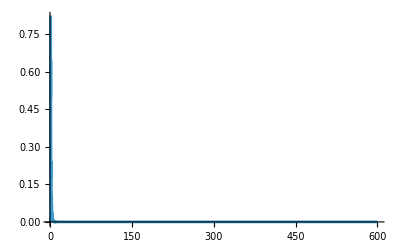

1/4 (-Cos[((-1+i+j-Nmodes+2 (i+j) Nmodes) π)/(2 (1+Nmodes))] Csc[((i+j) π)/(2 (1+Nmodes))]+Csc[((i-j) π)/(2 (1+Nmodes))] Sin[((i-j) (1+2 Nmodes) π)/(2 (1+Nmodes))])

```mathematica
(* leading order multiplier*)
Nmodes=600;
(*LogPlot[Sin[π/(Nmodes+1)] Sin[(Nmodes  π)/(Nmodes+1)] Sin[π/(Nmodes+1)] Sin[(Nmodes  π)/(Nmodes+1)] Sin[π/(Nmodes+1)] Sin[(Nmodes  π)/(Nmodes+1)] Sin[π/(Nmodes+1)] Sin[(Nmodes  π)/(Nmodes+1)],{Nmodes,1,10},PlotRange->All]*)

s[i_,p_,j_,q_,k_,m_,n_,r_]:=Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)] Sin[(p m π)/(Nmodes+1)] Sin[(j m π)/(Nmodes+1)] Sin[(p n π)/(Nmodes+1)] Sin[(q n π)/(Nmodes+1)] Sin[(i r π)/(Nmodes+1)] Sin[(q r π)/(Nmodes+1)];

Plot[s[i=300,p=1,j=Nmodes,q=Nmodes,k=1,m=1,n=1,r=1],{Nmodes,1,600},PlotRange->All]
```

```mathematica
Nmodes=10;
s[i_,j_,k_,m_]:=Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)] Sin[(i m π)/(Nmodes+1)] Sin[(j m π)/(Nmodes+1)] ;
λ[m_]:= 2 Sqrt[δ σ] Cos[(m π)/(Nmodes+1)]; (*δ=χ-g,σ=χ+g*)
(* first diagonal element, lowest power of N has the largest coefficient *)
δ=1;σ=2;t=10;
Plot[Sum[s[i=5,j,m,k] Exp[t (λ[m]+λ[k])],{m,1,Nmodes},{k,1,Nmodes}],{j,1,Nmodes},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Nmodes^2/4 Table[(BesselI[i-j,2 t Sqrt[δ σ]]-BesselI[i+j,2 t Sqrt[δ σ]])^2,{j,1,Nmodes}]]
```

-Graphics-

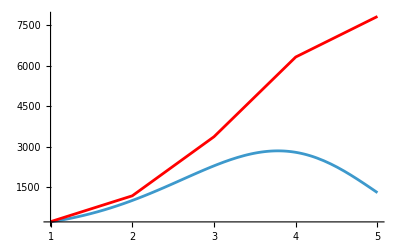

3.25315

```mathematica
Clear[i,j,t,δ,σ];
Nmodes=5;i=5;t=1;δ=1;σ=7;

Show[

Plot[Sum[s[i,j,m,k] Exp[t (λ[m]+λ[k])],{m,1,Nmodes},{k,1,Nmodes}],{j,1,Nmodes},PlotRange->All],

ListLinePlot[ Nmodes^2/4 Table[(BesselI[i-j,2 t Sqrt[δ σ]]-BesselI[i+j,2 t Sqrt[δ σ]])^2,{j,1,Nmodes}],PlotStyle->{Red},PlotRange->All]



]

2 Sqrt[t Sqrt[σ δ]]//N
```

```mathematica
10
```

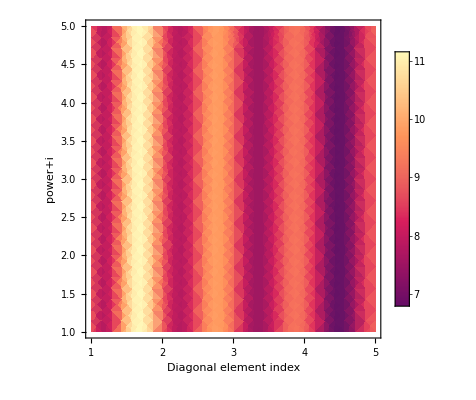

```mathematica
Nmodes=5;
δ=1;σ=2;t=0;
DensityPlot[Sum[(σ/δ)^(j-i) s[i,j,m,k] Exp[t (λ[m]+λ[k])],{m,1,Nmodes},{k,1,Nmodes},{j,1,Nmodes}],{i,1,Nmodes},{j,1,Nmodes},PlotLegends->Automatic,FrameLabel->{"Diagonal element index","power+i"}]
```

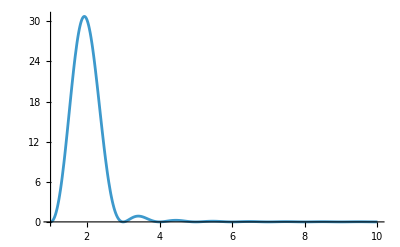

```mathematica
(* second diagonal element *)
Nmodes=10;
Plot[Sum[s[i=2,j,m,k],{m,1,Nmodes},{k,1,Nmodes}],{j,1,Nmodes},PlotRange->All]
```

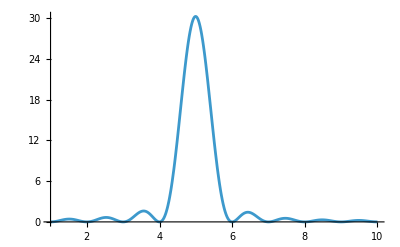

```mathematica
(* 5th diagonal element *)
Plot[Sum[s[i=5,j,m,k],{m,1,Nmodes},{k,1,Nmodes}],{j,1,Nmodes},PlotRange->All]
```

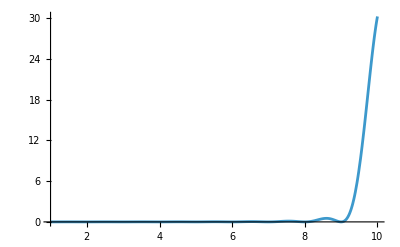

```mathematica
(* last diagonal element *)
Plot[Sum[s[i=Nmodes,j,m,k],{m,1,Nmodes},{k,1,Nmodes}],{j,1,Nmodes},PlotRange->All]
```

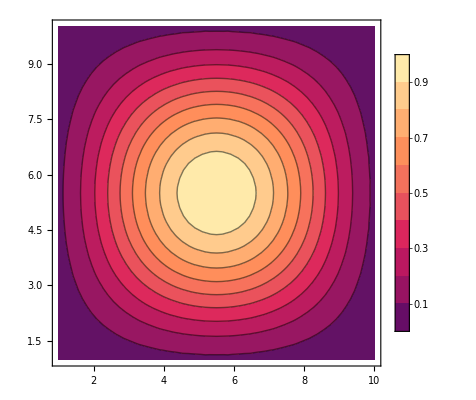

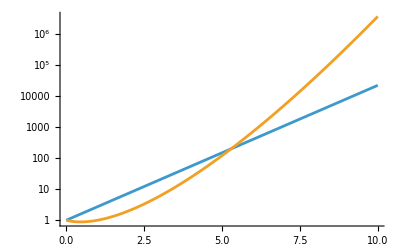

```mathematica
ContourPlot[s[i,j,k=1,m=1],{i,1,Nmodes},{j,1,Nmodes},PlotLegends->Automatic]
LogPlot[{Exp[n],n!},{n,0,10}]
```

```mathematica
FnNormal[Nmodes_,g_,χ_,t_]:=Module[{},
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}];
x=Table[((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{k,1,Nmodes},{h,1,Nmodes}];
y=Table[((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{h,1,Nmodes},{k,1,Nmodes}];
tr=Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//N;

nout=1/2 Tr[(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x],x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]]-Nmodes//N;

Fcov=-1/2 tr-Nmodes;
Fcov/nout
]
```

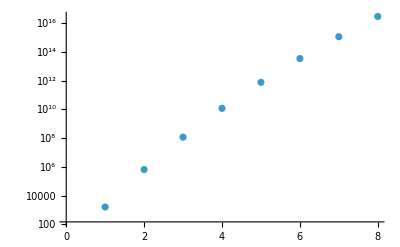

```mathematica
Clear[χ,g,t]
F2ep=(4 (t^2 χ^2+t^4 χ^4))/(t^2 χ^2);
F3ep=(32 (2+t^2 χ^2) (t χ+t^3 χ^3)^2)/(16 t^2 χ^2+8 t^4 χ^4);
F4ep=(48 t^2 χ^2+16/81 t^4 χ^4 (729+900 t^2 χ^2+522 t^4 χ^4+144 t^6 χ^6+16 t^8 χ^8))/(12 t^2 χ^2+8 t^4 χ^4+(16 t^6 χ^6)/9);
F5ep=(4 (3+t^2 χ^2) (108+315 t^2 χ^2+t^4 χ^4 (387+237 t^2 χ^2+77 t^4 χ^4+13 t^6 χ^6+t^8 χ^8)))/(9 (36+27 t^2 χ^2+8 t^4 χ^4+t^6 χ^6));
F6ep=(225 (80 t^2 χ^2+272 t^4 χ^4+(32 t^6 χ^6 (641250+523125 t^2 χ^2+261450 t^4 χ^4+t^6 χ^6 (84300+17800 t^2 χ^2+2425 t^4 χ^4+200 t^6 χ^6+8 t^8 χ^8)))/50625))/(4 t^2 χ^2 (1125+900 t^2 χ^2+300 t^4 χ^4+50 t^6 χ^6+4 t^8 χ^8));
F7ep=(96 t^2 χ^2+336 t^4 χ^4+(4672 t^6 χ^6)/9+(4000 t^8 χ^8)/9+(16 t^10 χ^10 (61017300+21951000 t^2 χ^2+5508000 t^4 χ^4+978075 t^6 χ^6+16 t^8 χ^8 (7650+657 t^2 χ^2+36 t^4 χ^4+t^6 χ^6)))/4100625)/(24 t^2 χ^2+(4 t^4 χ^4 (10125+3600 t^2 χ^2+675 t^4 χ^4+72 t^6 χ^6+4 t^8 χ^8))/2025);
F8ep=(112 t^2 χ^2+400 t^4 χ^4+(5696 t^6 χ^6)/9+(5024 t^8 χ^8)/9+(64 t^10 χ^10 (47827739925+18154801350 t^2 χ^2+4931879400 t^4 χ^4+987189525 t^6 χ^6+4 t^8 χ^8 (36900675+t^2 χ^2 (4124673+340452 t^2 χ^2+20090 t^4 χ^4+784 t^6 χ^6+16 t^8 χ^8))))/9845600625)/(28 t^2 χ^2+24 t^4 χ^4+(80 t^6 χ^6)/9+(16 t^8 χ^8)/9+(16 t^10 χ^10)/75+(32 t^12 χ^12)/2025+(64 t^14 χ^14)/99225);
F9ep=(128 t^2 χ^2+464 t^4 χ^4+(2240 t^6 χ^6)/3+672 t^8 χ^8+(86336 t^10 χ^10)/225+(101504 t^12 χ^12)/675+(4229632 t^14 χ^14)/99225+(16 t^16 χ^16 (5574460500+909033300 t^2 χ^2+115190964 t^4 χ^4+11381328 t^6 χ^6+t^8 χ^8 (872004+50960 t^2 χ^2+2192 t^4 χ^4+64 t^6 χ^6+t^8 χ^8)))/9845600625)/(32 t^2 χ^2+28 t^4 χ^4+(32 t^6 χ^6)/3+(4 t^8 χ^8 (55125+7056 t^2 χ^2+588 t^4 χ^4+32 t^6 χ^6+t^8 χ^8))/99225);

g=1;χ=2;t=10;
Show[ListLogPlot[{F2ep,F3ep,F4ep,F5ep,F6ep,F7ep,F8ep,F9ep}],ListLinePlot[{F2,F3,F4,F5,F6,F7},PlotStyle->Red]]
```

```mathematica
Nmodes=2;g=1;χ=2;t=1;
F2=FnNormal[Nmodes,g,χ,t]
Nmodes=3;
F3=FnNormal[Nmodes,g,χ,t]
Nmodes=4;
F4=FnNormal[Nmodes,g,χ,t]
Nmodes=5;
F5=FnNormal[Nmodes,g,χ,t]
Nmodes=6;
F6=FnNormal[Nmodes,g,χ,t]
```

43.9721

221.763

524.371

852.607

1128.73

```mathematica
Nmodes=7;
F7=FnNormal[Nmodes,g,χ,t]
Nmodes=8;
F8=FnNormal[Nmodes,g,χ,t]
```

1331.41

1473.04

20.

100.

284.158

554.148

844.827

1099.13

1295.19

1437.8

1540.78

1616.76

1674.6

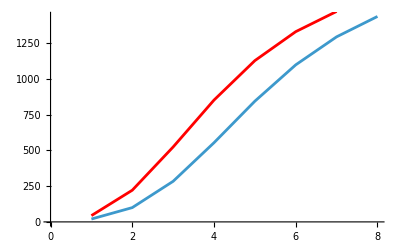

```mathematica
Nmodes=2;g=1;χ=2;t=1;
F2EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=3;
F3EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=4;
F4EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=5;
F5EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=6;
F6EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=7;
F7EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=8;
F8EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=9;
F9EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=10;
F10EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=11;
F11EP=QFInoDisp[Nmodes,χ,χ]//N
Nmodes=12;
F12EP=QFInoDisp[Nmodes,χ,χ]//N

Show[ListLinePlot[{F2EP,F3EP,F4EP,F5EP,F6EP,F7EP,F8EP,F9EP}],ListLinePlot[{F2,F3,F4,F5,F6,F7,F8},PlotStyle->Red]]
```

```mathematica
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Eigenvalues[S]
```

{(ⅇ^(-t √(-g^2+χ^2)) (g^2-χ^2))/((g-χ) (g+χ)),(ⅇ^(-t √(-g^2+χ^2)) (g^2-χ^2))/((g-χ) (g+χ)),(ⅇ^(t √(-g^2+χ^2)) (g^2-χ^2))/((g-χ) (g+χ)),(ⅇ^(t √(-g^2+χ^2)) (g^2-χ^2))/((g-χ) (g+χ))}

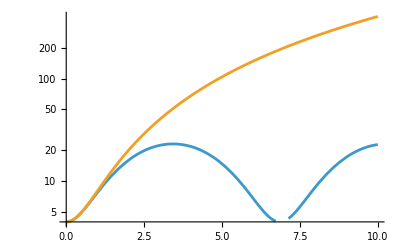

```mathematica
Clear[t,g,χ]
Nmodes=2;
g=1.1;χ=1;
LogPlot[{QFInoDisp[Nmodes,g,χ],QFInoDisp[Nmodes,χ,χ]},{t,0,10}]
```

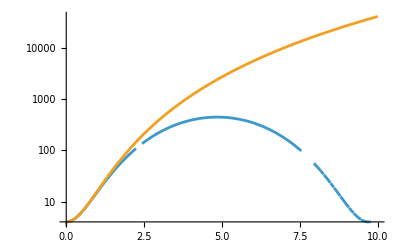

```mathematica
Clear[t,g,χ]
Nmodes=3;
g=1.1;χ=1;
LogPlot[{QFInoDisp[Nmodes,g,χ],QFInoDisp[Nmodes,χ,χ]},{t,0,10}]
```

```mathematica
Nmodes=4;
F4EP=QFInoDisp[Nmodes,χ,χ]
F4=QFInoDisp[Nmodes,g,χ]//N
```

416860/1467

$Aborted